# Confluent Set Substitution Systems

Maksim Piskunov

Mentor: Jonathan Gorard

We examined confluent set substitution systems using SetReplace package. We specifically obtained three results. First, we looked into applying critical pair completion idea from automated theorem proving to get quantum behavior. We did not explicitly reproduce any quantum effects, however, we found several possible directions to explore. Second, we emulated elementary cellular automata with non-overlapping set substitution systems, which demonstrates their universality. Finally, we performed am exhaustive search of the smallest non-overlapping set substitution systems up-to system size 14 (i.e., number of atoms in the initial condition and rules), but did not find any complex behavior.

#### Initialization Code

```mathematica
With[{version = "Version" /. PacletInformation["SetReplace"]},
	If[version =!= "0.1.9" &&
			ChoiceDialog["SetReplace 0.1.9 paclet needs to be installed. " <>
			If[version =!= "Version",
				"Your current version " <> version <> " will be removed. ",
				""] <>
			"Proceed?"],
		If[version =!= "Version",
			PacletUninstall["SetReplace"]];
		PacletInstall[
			"https://github.com/maxitg/SetReplace/releases/download/0.1.9/" <>
				"SetReplace-0.1.9.paclet"]]];
<< SetReplace`;
ParallelEvaluate[<< SetReplace`];
```

## Critical Pair Completion

#### Code

##### multiwayGraph

```mathematica
ClearAll[multiwayGraph];
```

```mathematica
Options[multiwayGraph] = {
	VertexLabels -> None,
	"HighlightVertices" -> Automatic,
	ImageSize -> Automatic};
```

```mathematica
multiwayGraph[rule_RuleDelayed, set_, steps_, o : OptionsPattern[]] :=
	multiwayGraph[{rule}, set, steps, o]
```

```mathematica
multiwayGraph[rules_List, set_, steps_, o : OptionsPattern[]] := Module[
		{graph},
	graph = NestGraph[
		Function[{g},
			Catenate[Function[{rule},
				$set[Sort @ SetReplace[g⟦1⟧, # -> (# /. rule)]] & /@
					SetCases[g⟦1⟧, rule⟦1⟧]] /@ rules]],
		$set[Sort @ set],
		steps,
		VertexLabels -> If[
			OptionValue[VertexLabels] === "HypergraphPlotTooltip",
			v_ :> Placed[
				HypergraphPlot[
					v⟦1⟧,
					GraphLayout -> "SpringElectricalEmbedding",
					VertexLabels -> "Name"],
				Tooltip],
			OptionValue[VertexLabels]],
		GraphLayout -> "SpringElectricalEmbedding"];
	HighlightGraph[
		graph,
		If[OptionValue["HighlightVertices"] === Automatic,
			VertexList[graph]⟦Position[VertexOutDegree[graph], 0]⟦All, 1⟧⟧,
			OptionValue["HighlightVertices"]],
		ImageSize -> OptionValue[ImageSize]]
]
```

##### branchCollapseRules

```mathematica
ClearAll[multiComplement, branchCollapseRules];
```

```mathematica
(* wxffles (stackexchange.com) *)
Clear[multiComplement];
multiComplement[a_, b_] := Module[{k},
	Join @@ (ConstantArray[First @ #, Max[Last @ #, 0]] & /@
		(Tally[a] /.
			(Tally[b] /. {e_, c_Integer} :> {e, k_Integer} -> {e, k - c})))
];
```

```mathematica
Options[branchCollapseRules] = {"Generality" -> "Anonymous"};

branchCollapseRules[graph_, rules_, o : OptionsPattern[]] := Module[
		{branchingStates, criticalPairs, rulesWithDuplicates},
	branchingStates = VertexList[graph]⟦
		Position[VertexOutDegree[graph], _ ?(# ≥ 2 &)]⟦All, 1⟧, 1⟧;
	criticalPairs = Select[IntersectingQ @@ (Flatten /@ #⟦All, 2⟧) &] @
		Catenate[Subsets[#, {2}] & /@
			Function[{state}, Catenate[Thread /@ (
				{#, SetCases[state, rules⟦#, 1⟧]} & /@ Range[Length[rules]])]] /@
			branchingStates];
	rulesWithDuplicates = Join[rules, Flatten[Function[{criticalPair},
		Module[{output, equivalentSubsets},
			output = #⟦2⟧ /. rules⟦#⟦1⟧⟧ & /@ criticalPair;
			equivalentSubsets = Join[
				multiComplement[criticalPair⟦#⟦1⟧, 2⟧, criticalPair⟦#⟦2⟧, 2⟧],
				output⟦#⟦2⟧⟧] & /@ {Range[2], Reverse @ Range[2]};
			RuleDelayed @@ {If[OptionValue["Generality"] === "Anonymous",
				Quiet[Replace[#⟦1⟧, x_ :> x_, {2}], RuleDelayed::rhs],
				#⟦1⟧], #⟦2⟧} & /@
					{equivalentSubsets, Reverse @ equivalentSubsets}
	]] /@ criticalPairs]];
	DeleteDuplicates[
		rulesWithDuplicates,
		Or @@ (Sort @ SetReplace[
				#⟦1, 1⟧ /. HoldPattern[Pattern][x_, Verbatim[_]] :> x,
				#⟦2⟧] === Sort @ #⟦1, 2⟧ & /@ {{#1, #2}, {#2, #1}}) &]
]
```

## Confluence and Relativity

In rewrite systems, the reference frame is determined by the order of rewrite events [NKS, 516]. In general, different order of rewrite events will yield different states of the system (i.e., rewrite events do not commute), which, at least if one only considers a single branch of the multiway system, does not reproduce special relativity.

To get around this issue, one idea is to only consider confluent rewrite systems, i.e., rewrite systems in which every divergent pair of rewrites (critical pair) can be converged to a single branch.

Furthermore, due to Newman’s lemma [Newman, 1942] local confluence is equivalent to global confluence, i.e., the possibility of converging a critical pair immediately is both sufficient and necessary for the global confluence (and therefore relativistic-ness) of the system.

One approach that is explored more in [sec.ca, sec.enum] is to begin with a rule that is locally confluent. However, in this section we explore a different approach based on real-time critical pair completion.

## Critical Pair Completion for Strings

Critical pair completion is an idea from automated theorem proving, where one starts evolving an arbitrary rewrite system as usual, but as soon as a critical pair is encountered, one adds a new bi-directional rule between the critical pair outputs.

For the sake of demonstration, consider the following non-confluent string rewrite system:

```mathematica
StringReplaceList["ABA",{"AB"->"X","BA"->"Y"}]
```

{XA,AY}

Note the critical pair arises because there are two ways to make a substitution, and once made, the system terminates. One can however add new rules to deal with this:

```mathematica
{"XA"->"AY","AY"->"XA"}
```

Now, the multiway network of this system is confluent, as there is a way to get from any final state to any other state

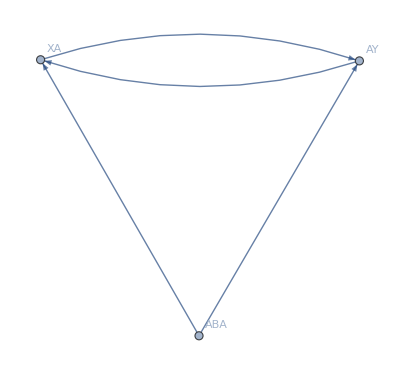

```mathematica
NestGraph[StringReplaceList[#,{,}]&,"ABA",2,]
```

## Critical Pair Completion for Networks

A similar approach can be used with networks. Consider for instance a particle represented as a single-vertex edge moving on a path graph.

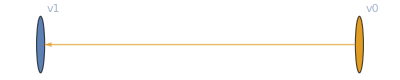
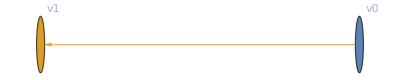
-Graphics-→-Graphics-

```mathematica
{{v0},{v0,v1}}->{{v1},{v0,v1}}//
```

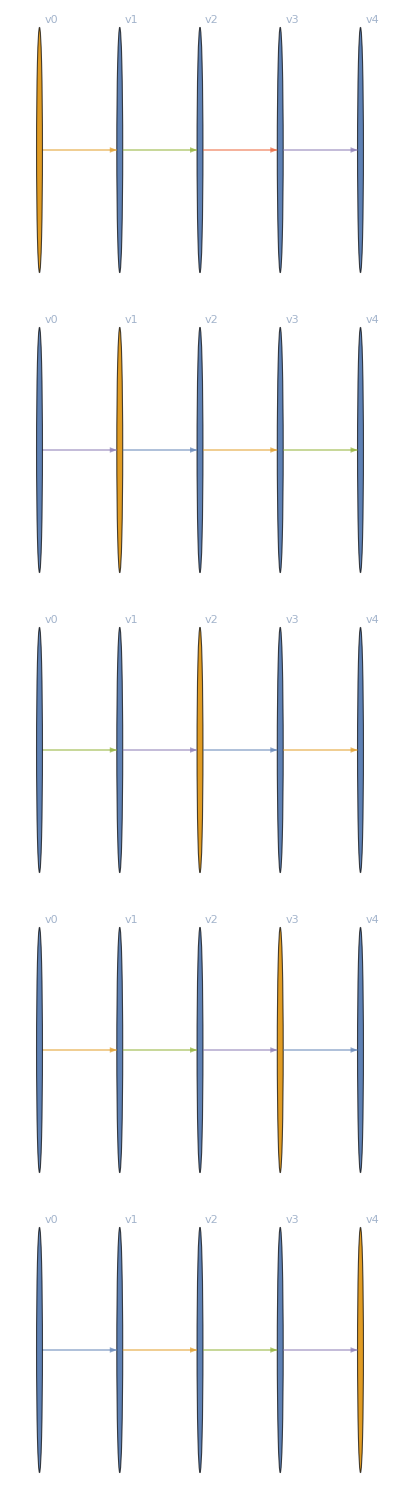

```mathematica
SetSubstitutionSystem[,{{v0},{v0,v1},{v1,v2},{v2,v3},{v3,v4}},4]//
```

This system is confluent already, in fact its multiway system is (mouseover to see the system)

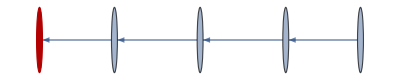

```mathematica
multiwayGraph[,,4,]
```

But what if we have a branching in the graph? What if we start with the initial condition

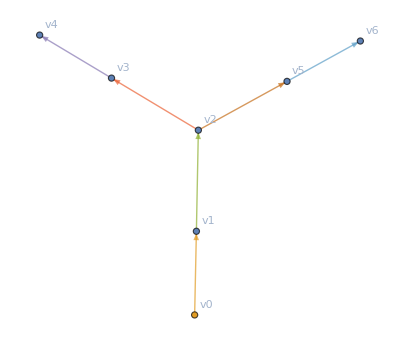

```mathematica
{{v0},{v0,v1},{v1,v2},{v2,v3},{v3,v4},{v2,v5},{v5,v6}}//
```

We then get a multiway system with two branches

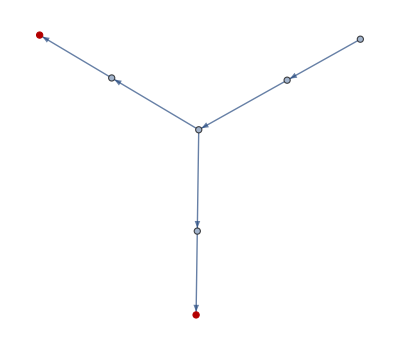

```mathematica
multiwayGraph[,,4,]
```

If we now perform a critical pair completion, we get an extra rule to move the particle back and force between branches

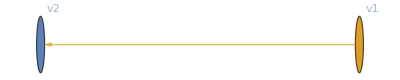
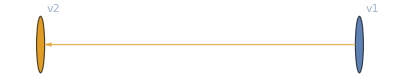
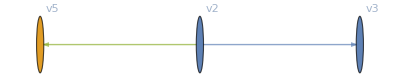
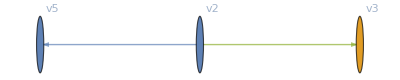
-Graphics-→-Graphics-
-Graphics-→-Graphics-

```mathematica
branchCollapseRules[,{}]//
```

and the multiway system becomes

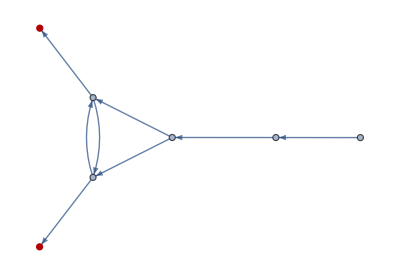

```mathematica
multiwayGraph[,,4,]
```

Note, a single collapse is insufficient to produce a confluent system, we need to perform a collapse again. After the next iteration we get

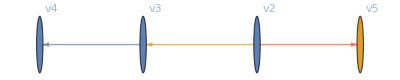
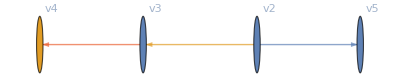
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-

```mathematica
Nest[branchCollapseRules[multiwayGraph[#,,4],#]&,,2]//
```

with the multiway system

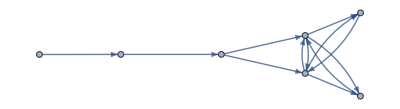

```mathematica
multiwayGraph[,,5,]
```

Note an interesting point that the rules created at this step allow one to go “back in time”. The loop created by this does not constitute a problem as it is not an actual time loop (in a sense of the causal network), but an evaluation loop, which the observer existing in any of the states of the system cannot see.

If we keep collapsing critical pairs until the fixed point, we will get the following rules

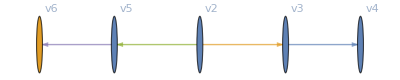
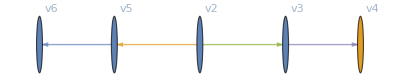
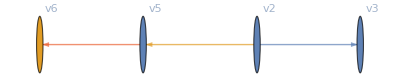
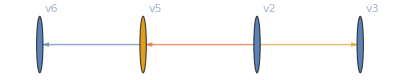
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-

```mathematica
FixedPoint[branchCollapseRules[multiwayGraph[#,,4],#]&,]//
```

and the multiway system that is a complete graph

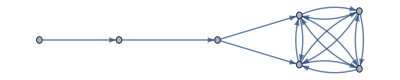

```mathematica
multiwayGraph[,,5,]
```

Note the multiway system we get after the first branching point is a complete graph. That is in fact a general feature. At first sight that seems like an issue, because the multiway graph loses all structure, therefore we don’t gain anything by performing critical pair completion.

## “Quantum” States

However, one has to realize that the rules used for completion are slightly more general than necessary to collapse the branches, and as such they might produce new states that did not exist in the system with original rules.

To see this happen, consider a graph with a branch that is not accessible in the original (classical) system

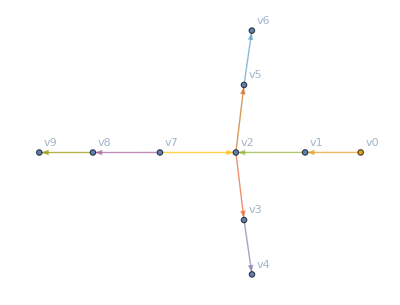

```mathematica
{{v0},{v0,v1},{v1,v2},{v2,v3},{v3,v4},{v2,v5},{v5,v6},{v7,v2},{v7,v8},{v8,v9}}//
```

In this system, the particle can never be at v7, v8 or v9 because they are not accessible by following directed edges from v0. However, after a single critical pair completion we get the multiway system that “leaks” into the forbidden branch

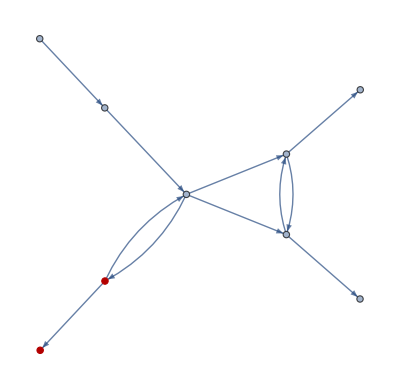

```mathematica
With[{multiway=multiwayGraph[,,5,]},HighlightGraph[multiway,Complement[VertexList[multiway],VertexList[]]]]
```

This effect resembles some similarity to quantum tunneling, in a sense that we can get classical-looking states which are nevertheless not accessible from the original system.

However, more investigation of more realistic systems is necessary to, for example, compare probabilities (which are not even clear how to compute in this model) of tunneling to what we expect from quantum mechanics.

## Other Ideas

A notable feature of the systems considered above is that multiway systems with original rules might significantly diverge. If one thinks of the original systems is classical, it would be plausible, for example, for the Earth to exist and not exist on different branches. Which essentially implies many-worlds interpretation of Quantum Physics. In other words, observer’s memory is different on different branches.

Another possibility is that all branching disappears by the observer’s scale, and the observer essentially sees the course-grained version of the multiway system.

In the description of “tunneling” above, we considered the first possibility. In what follows, we will only examine non-overlapping systems, which is the simplest case of the second possibility.

## Simulating Cellular Automata

## Problem Definition

To begin our study of non-overlapping systems, we will demonstrate their universality by simulating rule 110 elementary cellular automaton (CA) with it.

Rule 110 if started with a single black cell produces a collection of interacting structures

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},500],]
```

-Graphics-

One can in fact use these interacting structures to demonstrate its universality [NKS, 675].

We will use this fact to in turn demonstrate the universality of non-overlapping set substitution systems.

## Finite Grid Cells Representation

We begin by simulating a CA with a finite grid. To achieve that we begin with a schematic representation of a CA cell

```mathematica
caBlock[id_String,neighborIDs_ : {_String, _String},color_Integer]:={
{cellCenter[id],"nextStepLeftNeighborInput",nextStepLeftNeighborInput[id]},
{cellCenter[id],"nextStepRightNeighborInput",nextStepRightNeighborInput[id]},
{cellCenter[id],"nextStep",nextStepCenter[id]},
{cellCenter[id],"inputFromLeftNeighbor",rightNeighborInput[neighborIDs⟦1⟧]},
{cellCenter[id],"inputFromRightNeighbor",leftNeighborInput[neighborIDs⟦2⟧]},
{cellCenter[id],color},

{leftNeighborInput[id],"nextStep",nextStepLeftNeighborInput[id]},
{leftNeighborInput[id],color},

{rightNeighborInput[id],"nextStep",nextStepRightNeighborInput[id]},
{rightNeighborInput[id],color}
}//Map[ToString,#,{2}]&
```

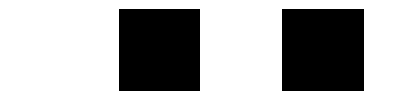
For a finite grid with 4 cells -Graphics- we get the following structure, where a subgraph corresponding to the first cell is highlighted in red, and its connections to the neighboring cells are in yellow.

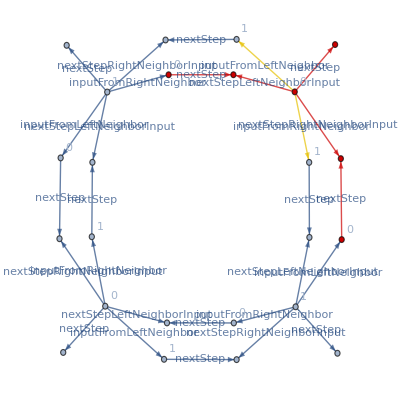

```mathematica
Join[caBlock["0",{"3","1"},0],caBlock["1",{"0","2"},1],caBlock["2",{"1","3"},0],caBlock["3",{"2","0"},1]]//
```

Note there are 6 vertices used to represent each cell: there are three colored ones for the current step. Out of these three, one is used to determine the color at the next step for the current cell, and two others are used by neighbors. Three other cells correspond to the cell at the next time step, and are not assigned any color.

## Color Updating Rules

We can then make a rule that would take as an input

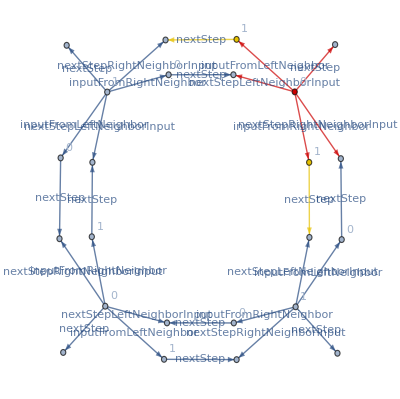

```mathematica
Join[caBlock["0",{"3","1"},0],caBlock["1",{"0","2"},1],caBlock["2",{"1","3"},0],caBlock["3",{"2","0"},1]]//HighlightGraph[(Graph[Cases[Labeled[_String,_]][#1],Cases[Labeled[_->_,_]][#1],GraphLayout->"SpringElectricalEmbedding"]&)[#1/.{{o_,p_,v_}:>Labeled[o->v,p],{o_,c_}:>Labeled[o,c]}],{{"cellCenter[0]","cellCenter[0]"->"nextStepCenter[0]","cellCenter[0]"->"nextStepLeftNeighborInput[0]","cellCenter[0]"->"nextStepRightNeighborInput[0]","cellCenter[0]"->"rightNeighborInput[3]","cellCenter[0]"->"leftNeighborInput[1]"},{"rightNeighborInput[3]","leftNeighborInput[1]","leftNeighborInput[1]"->"nextStepLeftNeighborInput[1]","rightNeighborInput[3]"->"nextStepRightNeighborInput[3]"}},ImageSize->Scaled[1]]&
```

Note there is no overlap between different rule applications (some vertices are not highlighted because we are only concerned with the overlap of edges here, and as vertices at the next step do not carry any information, we do not need to associate any additional edges to them apart from highlighted references).

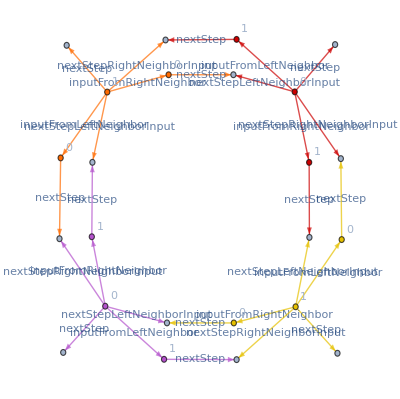

```mathematica
Join[caBlock["0",{"3","1"},0],caBlock["1",{"0","2"},1],caBlock["2",{"1","3"},0],caBlock["3",{"2","0"},1]]//HighlightGraph[(Graph[Cases[Labeled[_String,_]][#1],Cases[Labeled[_->_,_]][#1],GraphLayout->"SpringElectricalEmbedding"]&)[#1/.{{o_,p_,v_}:>Labeled[o->v,p],{o_,c_}:>Labeled[o,c]}],Table[{cellCenter[Mod[k,4]],cellCenter[Mod[k,4]]->nextStepCenter[Mod[k,4]],cellCenter[Mod[k,4]]->nextStepLeftNeighborInput[Mod[k,4]],cellCenter[Mod[k,4]]->nextStepRightNeighborInput[Mod[k,4]],cellCenter[Mod[k,4]]->rightNeighborInput[Mod[k-1,4]],cellCenter[Mod[k,4]]->leftNeighborInput[Mod[k+1,4]],rightNeighborInput[Mod[k-1,4]],leftNeighborInput[Mod[k+1,4]],leftNeighborInput[Mod[k+1,4]]->nextStepLeftNeighborInput[Mod[k+1,4]],rightNeighborInput[Mod[k-1,4]]->nextStepRightNeighborInput[Mod[k-1,4]]},{k,0,3}]/.{k:_Symbol[_Integer]:>ToString[k]},ImageSize->Scaled[1]]&
```

These rule inputs have 5 tentacles going from the main (middle) cell vertex: three point to the next time-step representation of the same cell, and at the rule application, they need to be assigned a particular color.

The other two point to the next step of the neighbors. The vertices these tentacles point two would not be updated, however, the references for the next step would be moved to the next steps of the neighbors (also blocking subsequent updates from happening until neighbors are updated as there is no color initially assigned to the next steps of the neighbor cells).

We can schematically write the rules as

```mathematica
caRules[rule_Integer]:=With[{oldLeft=#⟦1⟧,oldMiddle=#⟦2⟧,oldRight=#⟦3⟧,newColor=#⟦4⟧},{
{cellCenter_,"inputFromLeftNeighbor",leftColorReference_},{leftColorReference_,"nextStep",nextStepLeftColorReference_},
{cellCenter_,"inputFromRightNeighbor",rightColorReference_},{rightColorReference_,"nextStep",nextStepRightColorReference_},
{cellCenter_,"nextStepLeftNeighborInput",nextStepLeftNeighborInput_},{cellCenter_,"nextStepRightNeighborInput",nextStepRightNeighborInput_},
{cellCenter_,"nextStep",nextStepCenter_},
{cellCenter_,#⟦2⟧},{leftColorReference_,#⟦1⟧},{rightColorReference_,#⟦3⟧}
}:>Module[{nextNextStepLeftNeighborInput,nextNextStepRightNeighborInput,nextNextStepCellCenter},{
{nextStepCenter,"inputFromLeftNeighbor",nextStepLeftColorReference},{nextStepCenter,"inputFromRightNeighbor",nextStepRightColorReference},
{nextStepCenter,"nextStep",nextNextStepCellCenter},{nextStepCenter,"nextStepLeftNeighborInput",nextNextStepLeftNeighborInput},{nextStepCenter,"nextStepRightNeighborInput",nextNextStepRightNeighborInput},
{nextStepCenter,newColor},{nextStepLeftNeighborInput,newColor},{nextStepRightNeighborInput,newColor},
{nextStepLeftNeighborInput,"nextStep",nextNextStepLeftNeighborInput},{nextStepRightNeighborInput,"nextStep",nextNextStepRightNeighborInput}
}]]&/@Map[ToString,1-Flatten/@Thread[{IntegerDigits[Range[0,7],2,3],1-IntegerDigits[rule,2,8]}],{2}];
```

For an example where both neighbors are white, and the center is black, we get this step where old edges are in gray, and the new edges are in red

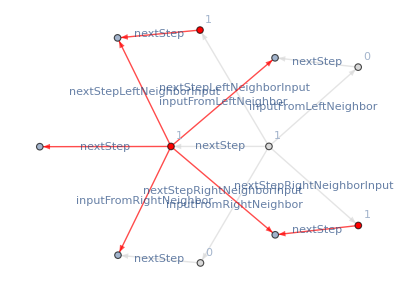

```mathematica
With[{states=SetReplace[,caRules[110],#]/.&/@{0,1}},HighlightGraph[[Union[Complement[states⟦1⟧,states⟦2⟧],Complement[states⟦2⟧,states⟦1⟧]]],{Style[Complement[states⟦1⟧,states⟦2⟧],LightGray],Style[Complement[states⟦2⟧,states⟦1⟧],Red]}]]
```

The entire graph after this step looks like this (with new edges highlighted in red), where one can see that the evolution of the same cell is blocked as there is no input from the neighbors

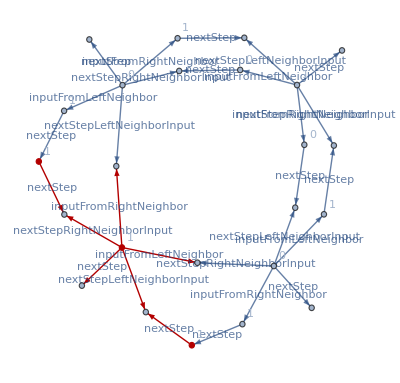

```mathematica
With[{states=SetReplace[,caRules[110],#]/.&/@{0,1}},HighlightGraph[[states⟦2⟧],Complement[states⟦2⟧,states⟦1⟧]]]
```

We can confirm that this system does not overlap after running it for 10 steps

```mathematica
SetSubstitutionSystem[caRules[110],,10,"CheckConfluence"->True]["ConfluentQ"]
```

Missing[Unknown]

Missing is returned because the code only checks for overlaps between edges at the current step, but it is possible for overlaps to occur between space-like pair of events even if some of the vertices for one of them are already deleted. For this particular system, it is easy to see that this is not occurring, hence it is in fact confluent.

## Localization

In the above, we simulated labeled edges and vertices by creating global vertices with names such as “inputFromLeftNeighbor”, “nextStep”, “1”, and representing labeled edges by hyperedges passing through these global vertices, i.e.,

```mathematica
Labeled[x->y,"nextStep"]<>{x,"nextStep",y}
```

However, it would be interesting to see if we can make the rules local, i.e., not involving any global vertices, and only depending on the vertices nearby the application site. This is indeed straightforward to do by making use of hyperedges with varying numbers of vertices, i.e.,

```mathematica
caLocalization={
{x_,"inputFromLeftNeighbor",y_}:>{x,x,y},
{x_,"inputFromRightNeighbor",y_}:>{x,y,x},
{x_,"nextStepLeftNeighborInput",y_}:>{x,x,x,y},
{x_,"nextStepRightNeighborInput",y_}:>{x,x,y,x},
{x_,"0"}:>{x},
{x_,"1"}:>{x,x},
{x_,"nextStep",y_}:>{x,y,y}
};
```

Now, we can localize both the rules and the initial condition to get the local evolution

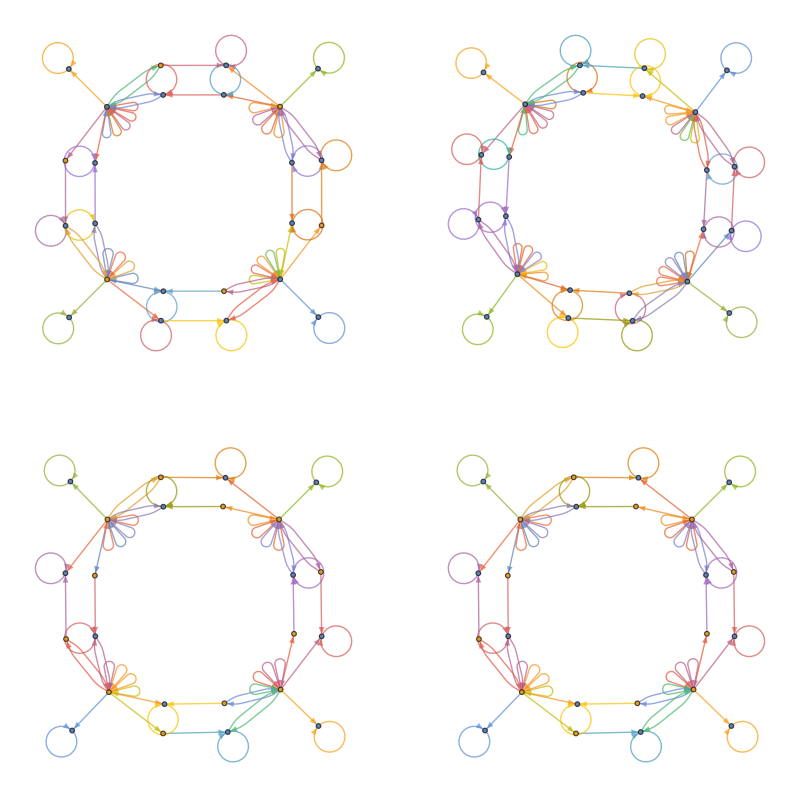

```mathematica
SetSubstitutionSystem[caRules[110]/.caLocalization,/.caLocalization,3]/@Range[0,3]//GraphicsGrid[Partition[HypergraphPlot[#,ImageSize->Scaled[1]]&/@#,2],ImageSize->Scaled[1]]&
```

To decode it, one can look at the number of loops in the cell centers: 4 loops means 0, 5 loops means 1, so decoding evolution from above, we get {1,0,1,0}, {1,1,1,1}, {0,0,0,0}, {0,0,0,0}, which matches the evolution of the actual CA:

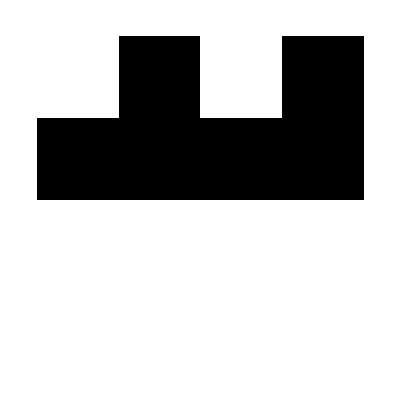

```mathematica
ArrayPlot[CellularAutomaton[110,{0,1,0,1},3],]
```

We can demonstrate that this system is confluent as well

```mathematica
SetSubstitutionSystem[caRules[110]/.caLocalization,/.caLocalization,10,"CheckConfluence"->True]["ConfluentQ"]
```

Missing[Unknown]

We can trivially extend this to any number of cells. For 10 cells, for instance, we get

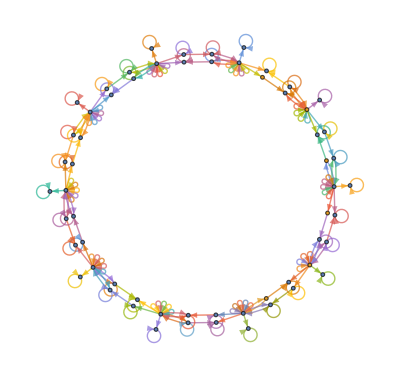

```mathematica
SetSubstitutionSystem[caRules[110]/.caLocalization,Join@@Table[caBlock[ToString[Mod[index,10]],ToString/@{Mod[index-1,10],Mod[index+1,10]},If[index==1,1,0]],{index,1,10}]/.caLocalization,8]//HypergraphPlot[#1[-1],ImageSize->Scaled[1]]&
```

that maps to {1,1,0,1,0,1,1,1,1,1} after 8 steps, same as rule 110 CA

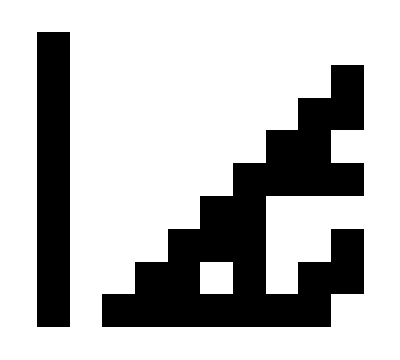

```mathematica
ArrayPlot[CellularAutomaton[110,{1,0,0,0,0,0,0,0,0,0},8],]
```

It is interesting to see how the causal network looks like in this case

```mathematica
["CausalNetwork"]//
```

-Graphics3D-

## Infinite Grid

Proving universality however requires an infinite grid. We can achieve that by initially attaching the ends of the grid by specially labeled “left/right end” cells, and then adding new rules to expand these ends.

Specifically, we can construct the following four-cell structure where one of the end cells is colored in red, and the grid cell it is attached to is colored in yellow

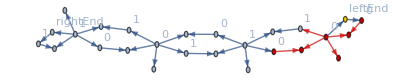

```mathematica
Join[Catenate[{caBlock["0",{"leftEnd","1"},0],caBlock["1",{"0","2"},1],caBlock["2",{"1","3"},0],caBlock["3",{"2","rightEnd"},1]}/.{"rightNeighborInput[leftEnd]"->"leftEnd","leftNeighborInput[rightEnd]"->"rightEnd"}],{{"leftEnd","inputFromRightNeighbor","leftNeighborInput[0]"},{"leftEnd","leftEnd"},{"rightEnd","inputFromLeftNeighbor","rightNeighborInput[3]"},{"rightEnd","rightEnd"}}]//
```

For the rule, we essentially need to replace the end cells with new white blocks connected to new ends, i.e.,

```mathematica
endExtensionRules={{{xCenter_,"inputFromLeftNeighbor",leftEnd_},{leftEnd_,"inputFromRightNeighbor",xLeftNeighborInput_},{leftEnd_,"leftEnd"}}:>Module[{cellCenter,nextStepLeftNeighborInput,nextStepRightNeighborInput,nextStepCenter,newLeftEnd,leftNeighborInput,rightNeighborInput},{
{cellCenter,"nextStepLeftNeighborInput",nextStepLeftNeighborInput},
{cellCenter,"nextStepRightNeighborInput",nextStepRightNeighborInput},
{cellCenter,"nextStep",nextStepCenter},
{cellCenter,"inputFromLeftNeighbor",newLeftEnd},
{newLeftEnd,"leftEnd"},
{newLeftEnd,"inputFromRightNeighbor",leftNeighborInput},
{cellCenter,"inputFromRightNeighbor",xLeftNeighborInput},
{cellCenter,"0"},
{leftNeighborInput,"nextStep",nextStepLeftNeighborInput},
{leftNeighborInput,"0"},
{rightNeighborInput,"nextStep",nextStepRightNeighborInput},
{rightNeighborInput,"0"},
{xCenter,"inputFromLeftNeighbor",rightNeighborInput}
}],};
```

Running these rules from a single black cell will extend the edges indefinitely

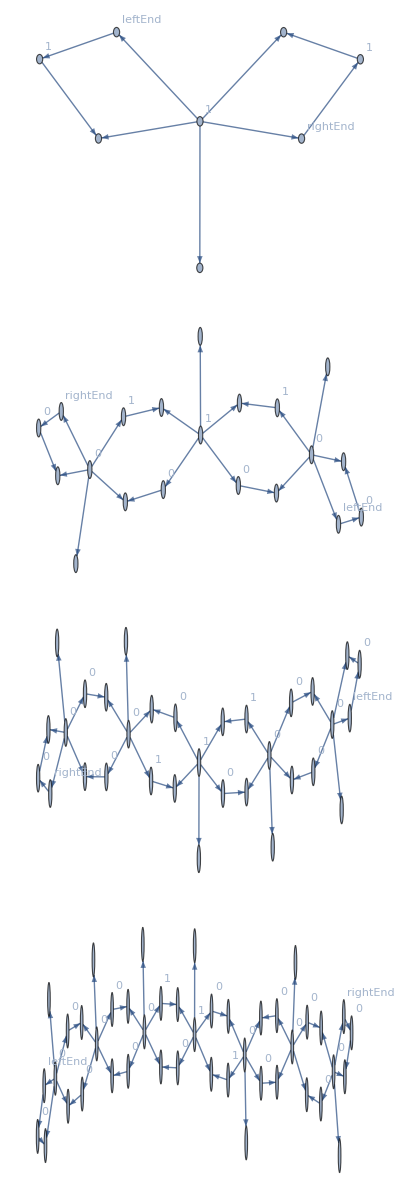

```mathematica
SetSubstitutionSystem[endExtensionRules,Join[caBlock["0",{"leftEnd","rightEnd"},1]/.{"rightNeighborInput[leftEnd]"->"leftEnd","leftNeighborInput[rightEnd]"->"rightEnd"},{{"leftEnd","inputFromRightNeighbor","leftNeighborInput[0]"},{"leftEnd","leftEnd"},{"rightEnd","inputFromLeftNeighbor","rightNeighborInput[0]"},{"rightEnd","rightEnd"}}],3]/@Range[0,3]//
```

Combining the two sets of rules together, we can get evolution of the CA on an infinite grid

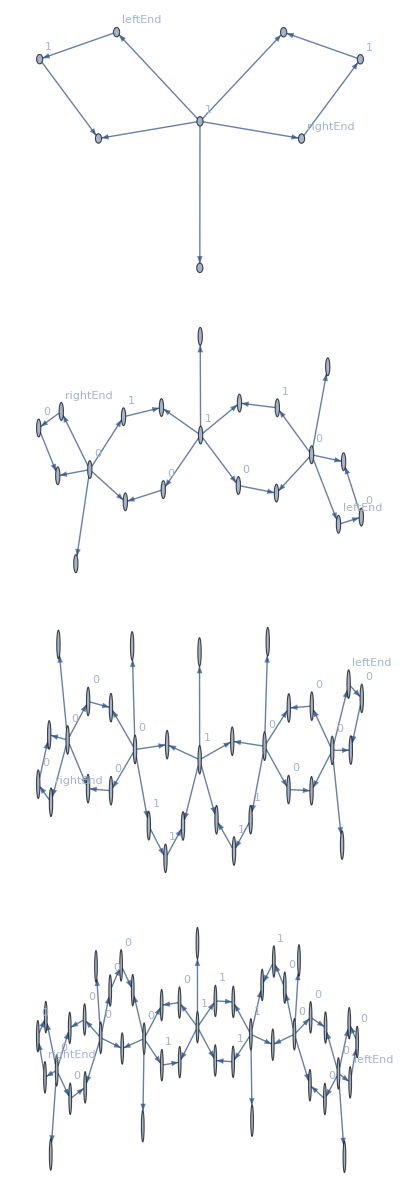

```mathematica
SetSubstitutionSystem[Join[endExtensionRules,caRules[110]],Join[caBlock["0",{"leftEnd","rightEnd"},1]/.{"rightNeighborInput[leftEnd]"->"leftEnd","leftNeighborInput[rightEnd]"->"rightEnd"},{{"leftEnd","inputFromRightNeighbor","leftNeighborInput[0]"},{"leftEnd","leftEnd"},{"rightEnd","inputFromLeftNeighbor","rightNeighborInput[0]"},{"rightEnd","rightEnd"}}],3]/@Range[0,3]//
```

Note, the evolution does not happen row-by-row, but instead we get past cones, for instance after 3 steps, we get the cells highlighted in blue

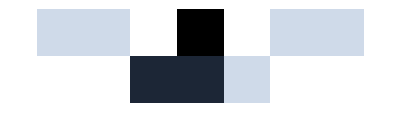

```mathematica
CellularAutomaton[110,{{1},0},{1,{-3,3}}]//
```

We can localize these rules similarly as before just adding new types of edges for left and right ends

```mathematica
caLocalizationInfinite={
{x_,"inputFromLeftNeighbor",y_}:>{x,x,y},
{x_,"inputFromRightNeighbor",y_}:>{x,y,x},
{x_,"nextStepLeftNeighborInput",y_}:>{x,x,x,y},
{x_,"nextStepRightNeighborInput",y_}:>{x,x,y,x},
{x_,"0"}:>{x},
{x_,"1"}:>{x,x},
{x_,"nextStep",y_}:>{x,y,y},
{x_,"leftEnd"}:>{x,x,x,x,x},
{x_,"rightEnd"}:>{x,x,x,x,x,x}
};
```

Running that for 3 steps, we then get

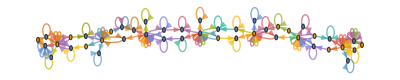

```mathematica
SetSubstitutionSystem[Join[endExtensionRules,caRules[110]]/.caLocalizationInfinite,/.caLocalizationInfinite,3][-1]//HypergraphPlot[#,ImageSize->Scaled[1]]&
```

After 10 steps we get

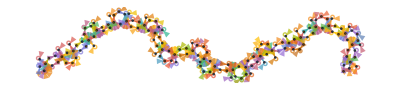

```mathematica
SetSubstitutionSystem[Join[endExtensionRules,caRules[110]]/.caLocalizationInfinite,/.caLocalizationInfinite,12][-1]//HypergraphPlot[#,ImageSize->Scaled[1],GraphLayout->"SpringEmbedding"]&
```

which corresponds to a slice of the CA

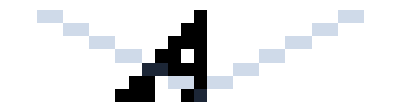

```mathematica
CellularAutomaton[110,{{1},0},{6,{-12,12}}]//
```

Of course, by changing the order at which the rules are applied, any space- (including light-)like slice of the CA can be obtained.

Note, it is straightforward to extend this approach to produce periodic initial conditions as well, which is what’s required for the proof of universality of rule 110.

We can finally show that this system is also confluent

```mathematica
SetSubstitutionSystem[Join[endExtensionRules,caRules[110]]/.caLocalizationInfinite,/.caLocalizationInfinite,12,"CheckConfluence"->True]["ConfluentQ"]
```

Missing[Unknown]

Thus we demonstrated that it is possible to construct a universal non-overlapping set substitution system.

## Enumeration